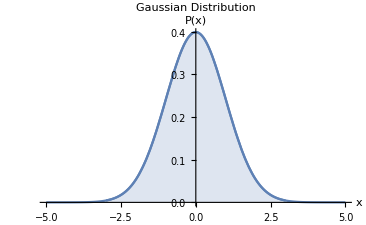

```mathematica
gaus[x_]:=1/Sqrt[2 Pi] Exp[-x^2/2];
p1 =Plot[gaus[x],{x,-5,5},AxesLabel->{"x","P(x)"},PlotLabel->"Gaussian Distribution"];
p2 = Plot[gaus[x], {x, -3, 3}, Filling->Axis];
Show[p1, p2]
```